```mathematica
ClearAll["Global`*"]
```

3-D P-C-R system
Where we examine scale and elasticities for the dimensionless version of the system (Rstar, Cstar, Pstar are dimensionless)

Scale parameters

```mathematica
scale$αr = FullSimplify[(aR*Rstar)/Rstar]
scale$αc = FullSimplify[ ((λC*(Rstar/(0.5+Rstar))*Cstar)+(σC*Cstar*Rstar))/Cstar]
scale$αp = FullSimplify[(w*λP*Cstar*Pstar)/Pstar]
```

aR

Rstar (λC/(0.5+Rstar)+σC)

Cstar w λP

Branching Parameters

```mathematica
branching$δ = FullSimplify[(1 - 1/scale$αc*(w*λP*P*C)/C)/.{P->Pstar,C->Cstar}]
branching$β = FullSimplify[(1/scale$αc*1/branching$δ*((μC*C)/C))/.{C->Cstar}]

branching$γ = FullSimplify[(1/scale$αp*((μP*P)/P))/.{P->Pstar}]
(*branching$κ = FullSimplify[1/scale$αr*((a*R^2)/R/.{R->Rstar})]*)
branching$κ = FullSimplify[(1-(1/scale$αr*((λC*(R/(0.5+R))*C)/R)))/.{R->Rstar,C->Cstar}]
(*branching$ϕ = FullSimplify[1/scale$αc*((λC*(R/(0.5+R))*C)/C/.{R->Rstar,C->Cstar})]*)
branching$ϕ=FullSimplify[(1-1/scale$αc*(σC*C*R)/C)/.{R->Rstar,C->Cstar}]
```

1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)

((0.5+Rstar) μC)/(-0.5 Pstar w λP+Rstar (λC-1. Pstar w λP+(0.5+Rstar) σC))

μP/(Cstar w λP)

1-(1. Cstar λC)/(aR (0.5+Rstar))

λC/(λC+(0.5+Rstar) σC)

Elasticities

```mathematica
elasticity$fr=FullSimplify[(Rstar/(aR*Rstar))*((D[aR*R,R])/.R->Rstar)]
```

1

```mathematica
elasticity$dr=FullSimplify[(Rstar/(aR*Rstar^2))*((D[aR*R^2,R])/.R->Rstar)]
```

2

```mathematica
elasticity$gr=FullSimplify[(Rstar/(λC*(Rstar/(0.5+Rstar))*Cstar))*((D[λC*(R/(0.5+R))*C,R])/.{R->Rstar,C->Cstar})]
```

0.5/(0.5+Rstar)

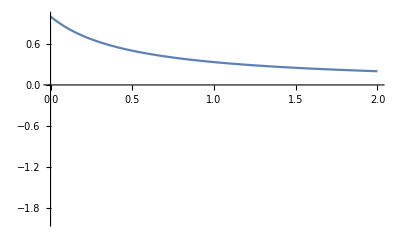

```mathematica
Plot[elasticity$gr,{Rstar,0,2},PlotRange->{-2,1}]
```

```mathematica
elasticity$gc=FullSimplify[(C/(λC*(R/(0.5+R))*C)/.{R->Rstar,C->Cstar})*((D[λC*(R/(0.5+R))*C,C])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
elasticity$hc=FullSimplify[(C/(σC*C*R)/.{R->Rstar,C->Cstar})*((D[σC*C*R,C])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
elasticity$hr=FullSimplify[(R/(σC*C*R)/.{R->Rstar,C->Cstar})*((D[σC*C*R,R])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
(*elasticity$sr=FullSimplify[(R/(σC*C)/.{R->Rstar,C->Cstar})*((D[σC*C,R])/.{R->Rstar,C->Cstar})]*)
```

```mathematica
elasticity$sc=FullSimplify[(C/(σC*C)/.{R->Rstar,C->Cstar})*((D[σC*C,C])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
elasticity$bc = FullSimplify[(C/(w*λP*P*C)/.{P->Pstar,C->Cstar})*((D[w*λP*P*C,C])/.{P->Pstar,C->Cstar})]
```

1

```mathematica
elasticity$bp = FullSimplify[(P/(w*λP*P*C)/.{P->Pstar,C->Cstar})*((D[w*λP*P*C,P])/.{P->Pstar,C->Cstar})]
```

1

```mathematica
elasticity$mc = FullSimplify[(C/(μC*C)/.{C->Cstar})*((D[μC*C,C])/.{C->Cstar})]
```

1

```mathematica
elasticity$tc = FullSimplify[(C/(σP*(1-C)*P)/.{P->Pstar,C->Cstar})*((D[σP*(1-C)*P,C])/.{P->Pstar,C->Cstar})]
```

Cstar/(-1+Cstar)

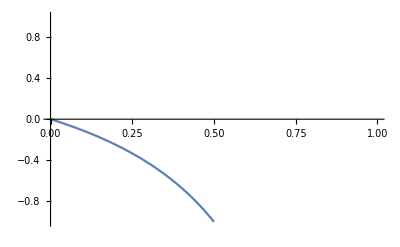

```mathematica
Plot[elasticity$tc,{Cstar,0,1},PlotRange->{-1,1}]
```

```mathematica
elasticity$tp = FullSimplify[(P/(σP*(1-C)*P)/.{P->Pstar,C->Cstar})*((D[σP*(1-C)*P,P])/.{P->Pstar,C->Cstar})]
```

1

```mathematica
elasticity$qp = FullSimplify[(P/(μP*P)/.{P->Pstar})*((D[μP*P,P])/.{P->Pstar})]
```

1

```mathematica
JacobianGeneral2D={
{ αc*(ϕ*gc+(1-ϕ)*hc-δ*(β*mc+(1-β)*sc)-(1-δ)*bc),αc*(ϕ*gr+(1-ϕ)*hr)},
{-αr*(1-κ)*gc,αr*(fr-κ*dr-(1-κ)*gr)}};
JacobianGeneral2D//MatrixForm
```

(αc (-bc (1-δ)-(sc (1-β)+mc β) δ+hc (1-ϕ)+gc ϕ) | αc (hr (1-ϕ)+gr ϕ)
-gc αr (1-κ) | αr (fr-gr (1-κ)-dr κ))

```mathematica
(*JacobianGeneral3D = {
{αp*(bp-γ*qp-(1-γ)*tp),αp*(bc-(1-γ)*tc),0},
{-αc*(1-δ)*bp, αc*(gc-δ*(β*mc+(1-β)*sc)-(1-δ)*bc),αc*(gr-δ*(1-β)*sr)},
{0,-αr*gc,αr*(fr-gr)}};
JacobianGeneral3D//MatrixForm*)
```

Solve Specific Model and Introduce Allometric Relationships

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->w*bP[M]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->w*bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[4]]
Rsol = R/.LVSS[[4]]
```

-1/(4 λ[M] σ[M]^2)α Y[M] (2 kRes (w bP[M]-λ[M]+μ[M])^2+kRes (3 w bP[M]-λ[M]+3 μ[M]) σ[M]+w bP[M] √(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2))-λ[M] √(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2))+μ[M] √(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2)))

(kRes (2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])+√(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2)))/(4 σ[M])

```mathematica
JacobianFullModel=({
{D[eqnC,C],D[eqnC,R]},
{D[eqnR,C],D[eqnR,R]}})/.{C->Csol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/ppmr_fit_table.csv"}],"csv"];
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ppmrint*M^ppmrslope;
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

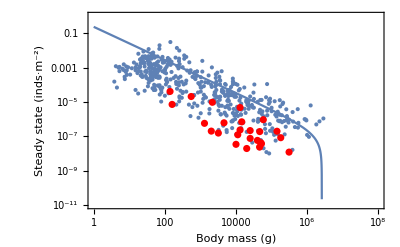

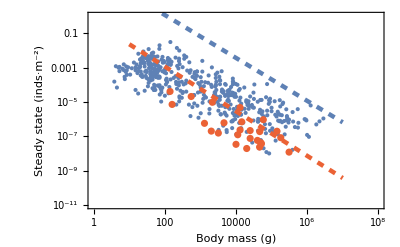

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.w->1,{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.w->1,{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.w->1,{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

Now repopulate the 2D Jacobian with the allometric relationships

```mathematica
JacobianSpecific2D =FullSimplify[JacobianGeneral2D/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
(*bc->elasticity$bc,*)
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp
}];
JacobianSpecific2D//MatrixForm
```

((1-1. bc) Pstar w λP | Rstar ((0.5 λC)/(0.5+1. Rstar)^2+1. σC)
-(1. Cstar λC)/(0.5+Rstar) | (-1. aR (0.5+1. Rstar)^2+Cstar (0.5+2. Rstar) λC)/(0.5+Rstar)^2)

```mathematica
JacobianAllometric2D =(JacobianSpecific2D/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
aR->α
};
```

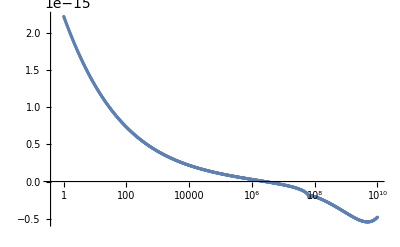

```mathematica
ListLogLinearPlot[
EigTable=Table[
{10^i,Det[(JacobianAllometric2D/.{M->(10^i),bc->1})]},
{i,0,10,0.01}]
]
```

```mathematica
ListLogLinearPlot[
EigTableFull=ParallelTable[
{10^i, Det[(JacobianFullModel/.{M->(10^i),w->1})]},
{i,0,10,0.01}],PlotRange->All
]
```

-Graphics-

```mathematica
TCbcGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,bc]]
```

{{bc→1/((-1+δ) (fr+gr (-1+κ)-dr κ))(-gc hr+gc hr κ+dr (hc+sc (-1+β) δ-mc β δ) κ+gr (-1+κ) ((sc+mc β-sc β) δ+hc (-1+ϕ))+(-dr hc κ+gc (hr+dr κ-hr κ)) ϕ+fr ((sc+mc β-sc β) δ+hc (-1+ϕ)-gc ϕ))}}

```mathematica
TCbcSpec = FullSimplify[TCbcGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
(*bc->elasticity$bc,*)
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

{{bc→(1. aR Pstar (0.5+1. Rstar)^3 w λP+Cstar λC (-0.5 Rstar λC-0.25 Pstar w λP+Pstar (-1.5-2. Rstar) Rstar w λP-1. Rstar (0.5+1. Rstar)^2 σC))/(Pstar (0.5+Rstar) w (aR (0.25+Rstar (1.+Rstar))+Cstar (-0.5-2. Rstar) λC) λP)}}

```mathematica
TCbcAllo = (TCbcSpec/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
aR->α};
```

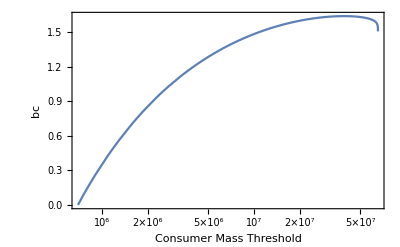

```mathematica
LogLinearPlot[(bc/.TCbcAllo)/.{w->1},{M,10^0,10^8},Frame->True,FrameLabel->{"Consumer Mass Threshold","bc"},PlotRange->{0,All}]
```

```mathematica
Plot3D[(bc/.TCbcAllo)/.M->10^i,{i,0,8},{w,0,2},PlotRange->{0,2},RegionFunction->Function[{i,w,z},z<1]]
```

-Graphics3D-

Let’s try this with another parameter... one that does not have a constant value (branching)

```mathematica
TCgcGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,gc]]
```

{{gc→((fr+gr (-1+κ)-dr κ) (bc-bc δ+(sc+mc β-sc β) δ+hc (-1+ϕ)))/(hr (-1+κ) (-1+ϕ)+(fr-dr κ) ϕ)}}

```mathematica
TCgcSpec = FullSimplify[TCgcGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
(*gc->elasticity$gc,*)
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

{{gc→(1. aR (0.5+1. Rstar)^2+Cstar (-0.5-2. Rstar) λC)/((0.5+Rstar) (aR (0.5+1. Rstar)-2. Cstar λC+Cstar (-0.5-1. Rstar) σC))}}

```mathematica
TCgcAllo = (TCgcSpec/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
aR->α};
```

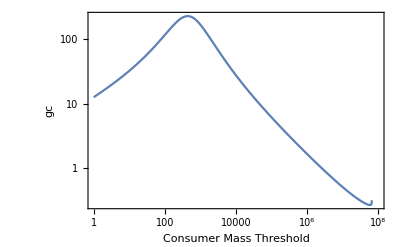

```mathematica
LogLogPlot[(gc/.TCgcAllo)/.w->1,{M,10^0,10^8},Frame->True,FrameLabel->{"Consumer Mass Threshold","gc"}]
```

```mathematica
TCscGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,sc]]
```

{{sc→1/((-1+β) δ (fr+gr (-1+κ)-dr κ))(gr hc-gc hr-gr mc β δ+dr hc κ-gr hc κ+gc hr κ-dr mc β δ κ+gr mc β δ κ-bc (-1+δ) (fr+gr (-1+κ)-dr κ)+(gr hc (-1+κ)-(dr hc+gc hr) κ+gc (hr+dr κ)) ϕ+fr (mc β δ+hc (-1+ϕ)-gc ϕ))}}

```mathematica
TCscSpec = FullSimplify[TCscGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
(*sc->elasticity$sc,*)
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

{{sc→(Cstar λC (0.25 Pstar w λP+0.25 μC+Rstar ((-1.-2. Rstar) λC+Pstar (1.5+2. Rstar) w λP+1.5 μC+2. Rstar μC-0.5 σC+(-2.5-3. Rstar) Rstar σC))+aR (-0.125 Pstar w λP-0.125 μC+Rstar (1. (0.5+1. Rstar)^2 λC+(-0.75+(-1.5-1. Rstar) Rstar) (Pstar w λP+μC)+1. (0.5+1. Rstar)^3 σC)))/((aR (0.25+Rstar (1.+Rstar))+Cstar (-0.5-2. Rstar) λC) (-0.5 Pstar w λP-0.5 μC+Rstar (λC-1. Pstar w λP-1. μC+(0.5+Rstar) σC)))}}

```mathematica
TCscAllo = (TCscSpec/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α};
```

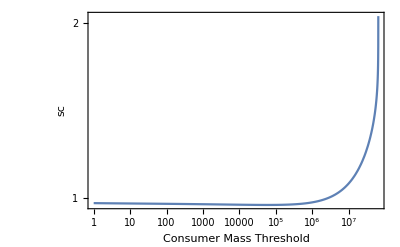

```mathematica
LogLogPlot[(sc/.TCscAllo)/.w->1,{M,10^0,10^9},Frame->True,FrameLabel->{"Consumer Mass Threshold","sc"},PlotRange->{0.5,All}]
```

```mathematica
TChcGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,hc]]
```

{{hc→(-bc+(bc+sc (-1+β)-mc β) δ+(gc (hr (-1+κ) (-1+ϕ)+(fr-dr κ) ϕ))/(fr+gr (-1+κ)-dr κ))/(-1+ϕ)}}

```mathematica
TChcSpec = FullSimplify[TChcGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
hr->elasticity$hr,
(*hc->elasticity$hc,*)
(*sr->elasticity$sr,*)
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

{{hc→(1. aR (0.5+1. Rstar)^3 σC+Cstar λC (0.5 λC+(-0.5-1. Rstar) Rstar σC))/((0.5+Rstar) (1. aR (0.5+1. Rstar)^2+Cstar (-0.5-2. Rstar) λC) σC)}}

```mathematica
TChcAllo = (TChcSpec/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α};
```

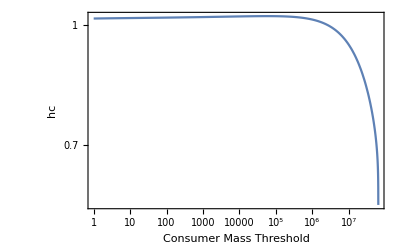

```mathematica
LogLogPlot[(hc/.TChcAllo)/.w->1,{M,10^0,10^9},Frame->True,FrameLabel->{"Consumer Mass Threshold","hc"},PlotRange->All]
```

```mathematica
TChrGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,hr]]
```

{{hr→(-((hc+bc (-1+δ)+sc (-1+β) δ-mc β δ) (fr+gr (-1+κ)-dr κ))+(fr (-gc+hc)+gr hc (-1+κ)+dr (gc-hc) κ) ϕ)/(gc (-1+κ) (-1+ϕ))}}

```mathematica
TChrSpec = FullSimplify[TChrGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
(*hr->elasticity$hr,*)
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

{{hr→-(0.5 λC)/((0.5+Rstar)^2 σC)}}

```mathematica
TChrAllo = (TChrSpec/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α};
```

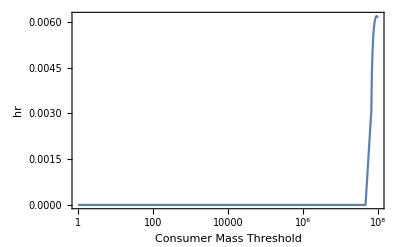

```mathematica
LogLinearPlot[Im[(hr/.TChrAllo)/.{w->1}],{M,10^0,10^8},Frame->True,FrameLabel->{"Consumer Mass Threshold","hr"},PlotRange->All]
```

```mathematica
TCfrGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,fr]]
```

{{fr→(-gc hr+gc hr κ+dr (hc+sc (-1+β) δ-mc β δ) κ-bc (-1+δ) (gr (-1+κ)-dr κ)+gr (-1+κ) ((sc+mc β-sc β) δ+hc (-1+ϕ))+(-dr hc κ+gc (hr+dr κ-hr κ)) ϕ)/(hc+bc (-1+δ)+sc (-1+β) δ-mc β δ+gc ϕ-hc ϕ)}}

```mathematica
TCfrSpec = FullSimplify[TCfrGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
(*fr->elasticity$fr,*)
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

FullSimplify::infd: Expression (-(1. Cstar λC)/(aR (0.5+Rstar))+(Pstar w (-(«1»)/(«1»)-«1») λP)/((Rstar «2»)/Plus[«1»]+«1»)+«1»-(«1»)/(«1»)+2 (1-(1. Cstar λC)/(aR (0.5+Rstar))) (1-((0.5+Rstar) μC (1-Pstar w λP Power[«2»]))/(Times[«4»]+Times[«2»])+(1-Pstar w λP Power[«2»]) (-1+Plus[«2»] μC Power[«2»])))/(1-(Pstar w λP)/(Rstar Power[«2»] λC+Rstar σC)-((0.5+Rstar) μC (1-(Pstar w λP)/Plus[«2»]))/(-0.5 Pstar w λP+Rstar Plus[«3»])+(1-(Pstar w λP)/Plus[«2»]) (-1+((0.5+Rstar) μC)/Plus[«2»])) simplified to ComplexInfinity.

{{fr→ComplexInfinity}}

This is a very constrained perspective... with one elasticity varied...
Can we try a more general formulation?
Do the same thing, but set bc = 1... and leave open branching parameters, which are all a function of steady states?

```mathematica
TCphigcGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,ϕ]]
```

{{ϕ→(-gc hr-(fr-gr) (hc+bc (-1+δ)+sc (-1+β) δ-mc β δ)+(gc hr+(dr-gr) (hc+bc (-1+δ)+sc (-1+β) δ-mc β δ)) κ)/(fr (gc-hc)+gr hc+dr hc κ-gr hc κ+gc hr κ-gc (hr+dr κ))}}

```mathematica
TCphigcSpec = FullSimplify[TCphigcGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
(*ϕ->branching$ϕ,*)
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
(*gc->elasticity$gc,*)
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

{{ϕ→-(1. Cstar gc (0.5+Rstar) λC)/(aR (1.-1. gc) (0.5+1. Rstar)^2+Cstar (-0.5-2. Rstar+gc (0.5+1. Rstar)) λC)}}

```mathematica
TCphigcAllo = (TCphigcSpec/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α};
```

```mathematica
MassTrajectory=ParallelTable[
allo$gc =(( elasticity$gc/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
aR->α
})/.M->10^i;
allo$ϕ =(( branching$ϕ/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
aR->α
})/.M->10^i;
Re[{i,allo$gc,allo$ϕ}],{i,5,8,0.01}];
```

```mathematica
Show[{
Plot3D[(ϕ/.TCphigcAllo)/.{M->10^i,w->1},{i,5,8},{gc,0.5,1.5},PlotRange->{0,1}],
ListPointPlot3D[MassTrajectory]
}]
```

-Graphics3D-

```mathematica
TCphibcGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,ϕ]]
```

{{ϕ→(-gc hr-(fr-gr) (hc+bc (-1+δ)+sc (-1+β) δ-mc β δ)+(gc hr+(dr-gr) (hc+bc (-1+δ)+sc (-1+β) δ-mc β δ)) κ)/(fr (gc-hc)+gr hc+dr hc κ-gr hc κ+gc hr κ-gc (hr+dr κ))}}

```mathematica
TCphibcSpec = FullSimplify[TCphibcGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
(*ϕ->branching$ϕ,*)
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
(*bc->elasticity$bc,*)
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

{{ϕ→(aR (-1.+1. bc) Pstar (0.5+1. Rstar)^3 w λP+Cstar λC (Rstar (0.5+1. Rstar) λC+Pstar (0.25+Rstar (1.5+2. Rstar)+bc (-0.25+(-1.5-2. Rstar) Rstar)) w λP+1. Rstar (0.5+1. Rstar)^2 σC))/(Cstar Rstar^2 λC (λC+(0.5+Rstar) σC))}}

```mathematica
TCphibcAllo = (TCphibcSpec/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α};
```

```mathematica
MassTrajectorybc=ParallelTable[
allo$bc =(( elasticity$bc/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
aR->α
})/.M->10^i;
allo$ϕ =(( branching$ϕ/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
aR->α
})/.M->10^i;
Re[{i,allo$bc,allo$ϕ}],{i,5,8,0.01}];
```

```mathematica
Show[{
Plot3D[(ϕ/.TCphibcAllo)/.{M->10^i,w->1},{i,5,8},{bc,0.5,1.5},PlotRange->{0,1}],
ListPointPlot3D[MassTrajectorybc]
}]
```

-Graphics3D-

```mathematica
TCphigcAllo/.{gc->1,M->1}
```

{{ϕ→(0.000607065 (0.5+0.835618 (23000 √(0.000104063 (0.0000130334+1.07048×10^-10 w)+(0.0000122634+2.14095×10^-10 w)^2)+23000 (0.0000122634+2.14095×10^-10 w))) (-0.00856045 √(0.000104063 (0.0000130334+1.07048×10^-10 w)+(0.0000122634+2.14095×10^-10 w)^2)+46000 (-3.72194×10^-7+1.07048×10^-10 w)^2+0.29918 (-3.21074×10^-7+3.21143×10^-10 w)+2.4621×10^-6 √(0.000104063 (0.0000130334+1.07048×10^-10 w)+(0.0000122634+2.14095×10^-10 w)^2) w))/(0.-0.000607065 (0.-0.835618 (23000 √(0.000104063 (0.0000130334+1.07048×10^-10 w)+(0.0000122634+2.14095×10^-10 w)^2)+23000 (0.0000122634+2.14095×10^-10 w))) (-0.00856045 √(0.000104063 (0.0000130334+1.07048×10^-10 w)+(0.0000122634+2.14095×10^-10 w)^2)+46000 (-3.72194×10^-7+1.07048×10^-10 w)^2+0.29918 (-3.21074×10^-7+3.21143×10^-10 w)+2.4621×10^-6 √(0.000104063 (0.0000130334+1.07048×10^-10 w)+(0.0000122634+2.14095×10^-10 w)^2) w))}}

```mathematica
Manipulate[
Show[{
Plot[(ϕ/.TCphigcAllo)/.{M->10^i,w->1},{gc,0.8,1.2},Frame->True,PlotRange->{0,1}],
ListPlot[Transpose[{MassTrajectory[[All,2]],MassTrajectory[[All,3]]}]]
}],
{i,0,8}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
MassTrajectory
```

{{0.337447,0.0202197},{0.337447,0.0202199},{0.337448,0.0202202},{0.337448,0.0202205},{0.337449,0.0202207},{0.337449,0.020221},{0.337449,0.0202212},{0.33745,0.0202215},{0.33745,0.0202218},{0.33745,0.020222},{0.337451,0.0202223},7979,{0.22078,0.0879268},{0.220759,0.0878296},{0.220738,0.0877329},{0.220716,0.0876367},{0.220694,0.0875409},{0.220672,0.0874455},{0.220649,0.0873506},{0.220625,0.0872561},{0.220601,0.087162},{0.220577,0.0870684},{0.220552,0.0869752}}
 |  |  |  |

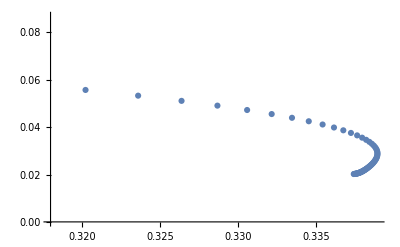

```mathematica
ListPlot[MassTrajectory]
```

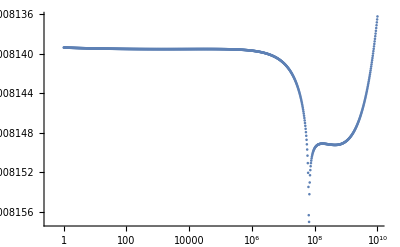

```mathematica
ListLogLinearPlot[
EigTable=Table[
Eig = Eigenvalues[(JacobianAllometric2D/.M->(10^i))];
RealEig = Re[Eig];
{10^i,Min[RealEig]},
{i,0,10,0.01}]
]
```

```mathematica
ListLogLinearPlot[
EigTable=Table[
{10^i,Det[(JacobianAllometric2D/.M->(10^i))]},
{i,0,10,0.01}]
]
```

-Graphics-

Compare the scaled model above to the full model

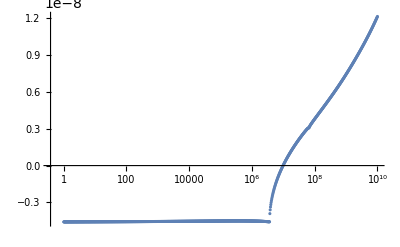

```mathematica
ListLogLinearPlot[
EigTableFull=ParallelTable[
EigFull = Eigenvalues[(JacobianFullModel/.{w->0.5,M->(10^i)})];
RealEigFull = Re[EigFull];
{10^i,Max[RealEigFull]},
{i,0,10,0.01}]
]
```

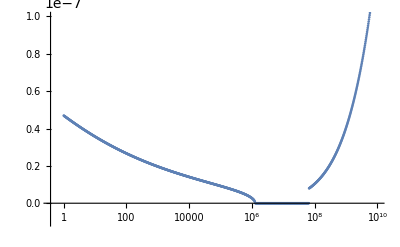

```mathematica
ListLogLinearPlot[
EigTableFull=ParallelTable[
EigFull = Eigenvalues[(JacobianFullModel/.M->(10^i))];
RealEigFull = Re[EigFull];
{10^i,Max[ Im[EigFull]]},
{i,0,10,0.01}],PlotRange->{-10^-8,10^-7}
]
```

```mathematica
ListLogLinearPlot[
EigTableFull=ParallelTable[
{10^i, Det[(JacobianFullModel/.M->(10^i))]},
{i,0,10,0.01}],PlotRange->All
]
```

-Graphics-

```mathematica
EigTable[[Flatten[Position[EigTableFull[[All,2]],Min[EigTableFull[[All,2]]]],1][[1]]]]
```

{2.5704×10^6,1.43419×10^-11}

How to important scale, branching, and elasticity parameters change with Consumer Mass?
alphac
alphar
fr
gr
delta
beta
sr

```mathematica
JacobianGeneral2D/.{gc->1,hc->1,hr->1,sc->1,bc->1,bp->1,mc->1,tp->1,qp->1,fr->1,dr->2}//MatrixForm
```

(0 | αc (1-ϕ+gr ϕ)
-αr (1-κ) | αr (1-gr (1-κ)-2 κ))

```mathematica
allo$αc = (scale$αc/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
allo$αr =( scale$αr/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
allo$β=( branching$β/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
allo$δ = (branching$δ/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
allo$κ =( branching$κ/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
allo$ϕ = (branching$ϕ/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
(*allo$fr = elasticity$fr/.{Rstar -> Rsol/kRes,Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),w->1,λC->λ[M],λP->λPred[OptPredMass[M]],μC->μ[M]};*)
allo$gr = (elasticity$gr/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
```

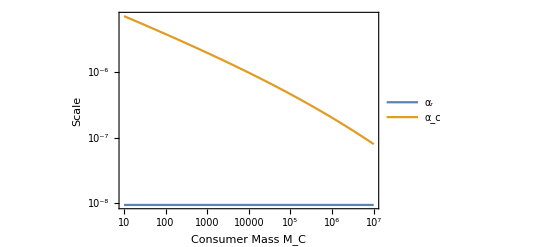

```mathematica
LogLogPlot[{allo$αr,allo$αc},{M,10^1,10^7},Frame->True,PlotLegends->{"α_r","α_c"},FrameLabel->{"Consumer Mass M_C","Scale"}]
```

```mathematica
allo$αr
```

8.13994×10^-6

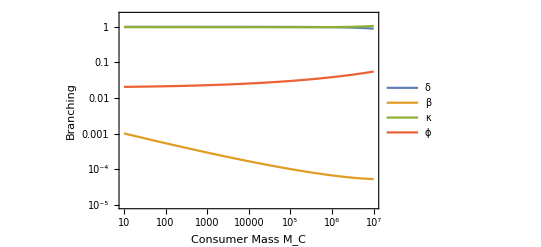

```mathematica
LogLogPlot[{
allo$δ,
allo$β,
allo$κ,
allo$ϕ},{M,10^1,10^7},Frame->True,PlotLegends->{"δ","β","κ","ϕ"},FrameLabel->{"Consumer Mass M_C","Branching"},PlotRange->{10^(-5),2}]
```

```mathematica
allo$β/.M->10^6
```

5.10613×10^6 μC

What are the bifurcation conditions for the Generalized Model?
Relate the scale

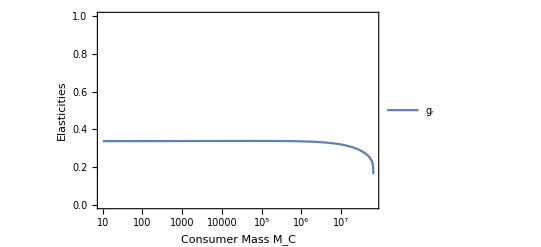

```mathematica
LogLinearPlot[{allo$gr},{M,10^1,10^8},Frame->True,PlotLegends->{"g_r"},FrameLabel->{"Consumer Mass M_C","Elasticities"},PlotRange->{0,1}]
```

```mathematica
allo$gr/.M->10000
```

0.338784

```mathematica
0.5/(1.5)
```

0.333333

```mathematica
FullSimplify[Solve[Det[(JacobianGeneral2D)]==0,w]]
```

{}

```mathematica
Det[JacobianGeneral2D]
```

-bc fr αc αr+bc gr αc αr+fr hc αc αr-gr hc αc αr+gc hr αc αr+bc fr αc αr δ-bc gr αc αr δ-fr sc αc αr δ+gr sc αc αr δ-fr mc αc αr β δ+gr mc αc αr β δ+fr sc αc αr β δ-gr sc αc αr β δ+bc dr αc αr κ-bc gr αc αr κ-dr hc αc αr κ+gr hc αc αr κ-gc hr αc αr κ-bc dr αc αr δ κ+bc gr αc αr δ κ+dr sc αc αr δ κ-gr sc αc αr δ κ+dr mc αc αr β δ κ-gr mc αc αr β δ κ-dr sc αc αr β δ κ+gr sc αc αr β δ κ+fr gc αc αr ϕ-fr hc αc αr ϕ+gr hc αc αr ϕ-gc hr αc αr ϕ-dr gc αc αr κ ϕ+dr hc αc αr κ ϕ-gr hc αc αr κ ϕ+gc hr αc αr κ ϕ

```mathematica
SpecDet = FullSimplify[Det[JacobianGeneral2D]]/.{gc->elasticity$gc,hc->elasticity$hc,hr->elasticity$hr,sc->elasticity$sc,bc->elasticity$bc,bp->elasticity$bp,mc->elasticity$mc,tp->elasticity$tp,qp->elasticity$qp,fr->elasticity$fr,dr->elasticity$dr,αr->scale$αr,κ->branching$κ,δ->branching$δ,gr->elasticity$gr,β->branching$β,αc->scale$αc,ϕ->branching$ϕ}
```

aR Rstar (λC/(0.5+Rstar)+σC) (1.-0.5/(0.5+Rstar)+(1. Cstar λC)/(aR (0.5+Rstar))-2 (1-(1. Cstar λC)/(aR (0.5+Rstar)))+(0.5 (1-(1. Cstar λC)/(aR (0.5+Rstar))))/(0.5+Rstar)-(Pstar w (1-(0.5 Cstar λC)/(aR (0.5+Rstar)^2)-2 (1-(1. Cstar λC)/(aR (0.5+Rstar)))) λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)+(λC (0.5/(0.5+Rstar)-(1. Cstar λC)/(aR (0.5+Rstar))-(0.5 (1-(1. Cstar λC)/(aR (0.5+Rstar))))/(0.5+Rstar)))/(λC+(0.5+Rstar) σC)+(0.5 (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)))/(0.5+Rstar)+2 (1-(1. Cstar λC)/(aR (0.5+Rstar))) (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC))-(0.5 (1-(1. Cstar λC)/(aR (0.5+Rstar))) (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)))/(0.5+Rstar)-((0.5+Rstar) μC (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)))/(-0.5 Pstar w λP+Rstar (λC-1. Pstar w λP+(0.5+Rstar) σC))+(1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)) (-1+((0.5+Rstar) μC)/(-0.5 Pstar w λP+Rstar (λC-1. Pstar w λP+(0.5+Rstar) σC))))

```mathematica
FullSimplify[Solve[SpecDet==0,w]]
```

{}

```mathematica
AlloSpecDet = (SpecDet/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes)
})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α
};
```

```mathematica
Show[{
Plot3D[AlloSpecDet/.M->10^i,{i,1,8},{w,0,2}(*,RegionFunction->Function[{i,ϕ,z},z>0]*)],
Plot3D[0,{i,0,8},{w,0,2},PlotStyle->Blue]
}]
```

-Graphics3D-

```mathematica
SpecDet
```

8.13994×10^-6 Rstar (λC/(0.5+Rstar)+σC) (1.-0.5/(0.5+Rstar)+(122851. Cstar λC)/(0.5+Rstar)-2 (1-(122851. Cstar λC)/(0.5+Rstar))+(0.5 (1-(122851. Cstar λC)/(0.5+Rstar)))/(0.5+Rstar)-(Pstar w (1-(61425.5 Cstar λC)/(0.5+Rstar)^2-2 (1-(122851. Cstar λC)/(0.5+Rstar))) λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)+(0.5 (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)))/(0.5+Rstar)+2 (1-(122851. Cstar λC)/(0.5+Rstar)) (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC))-(0.5 (1-(122851. Cstar λC)/(0.5+Rstar)) (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)))/(0.5+Rstar)-((0.5+Rstar) μC (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)))/(-0.5 Pstar w λP+Rstar (λC-1. Pstar w λP+(0.5+Rstar) σC))+(1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)) (-1+((0.5+Rstar) μC)/(-0.5 Pstar w λP+Rstar (λC-1. Pstar w λP+(0.5+Rstar) σC)))+(0.5/(0.5+Rstar)-(122851. Cstar λC)/(0.5+Rstar)-(0.5 (1-(122851. Cstar λC)/(0.5+Rstar)))/(0.5+Rstar)) ϕ)

```mathematica
TCSpecDet=FullSimplify[Solve[SpecDet==0,gr]]
```

{}

```mathematica
MassTrajectory$grvsM=ParallelTable[Re[{10^i,allo$gr}/.M->10^i],{i,0,8,0.01}];
```

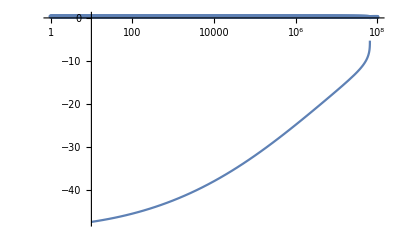

```mathematica
Show[{
LogLinearPlot[gr/.TCSpecDet/.{λC->λ[M],σC->σ[M],Rstar->Rsol/kRes},{M,10^1,10^8},PlotRange->{All,10}],
ListLogLinearPlot[MassTrajectory$grvsM]
}]
```

```mathematica
MassTrajectory=ParallelTable[Re[{allo$ϕ,allo$gr}/.M->10^i],{i,0,8,0.01}];
```

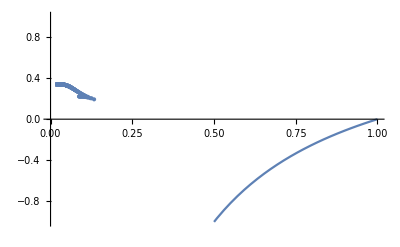

```mathematica
Show[{
Plot[gr/.(TCSpecDet)/.M->1,{ϕ,0,1},PlotRange->{-1,1}],
ListPlot[MassTrajectory]
}]
```

```mathematica
(FullSimplify[Det[JacobianGeneral2D]]/.{gc->elasticity$gc,hc->elasticity$hc,hr->elasticity$hr,sc->elasticity$sc,bc->elasticity$bc,bp->elasticity$bp,mc->elasticity$mc,tp->elasticity$tp,qp->elasticity$qp,fr->elasticity$fr,dr->elasticity$dr,αr->allo$αr,gr->elasticity$gc,δ->branching$δ,κ->branching$κ,(*ϕ->branching$ϕ,*)αc->scale$αc,β->branching$β})
```

8.13994×10^-6 Rstar (λC/(0.5+Rstar)+σC) (2.-2 (1-(122851. Cstar λC)/(0.5+Rstar))-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)-(Pstar w (1-(122851. Cstar λC)/(0.5+Rstar)-2 (1-(122851. Cstar λC)/(0.5+Rstar))) λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)+(1-(122851. Cstar λC)/(0.5+Rstar)) (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC))-((0.5+Rstar) μC (1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)))/(-0.5 Pstar w λP+Rstar (λC-1. Pstar w λP+(0.5+Rstar) σC))+(1-(Pstar w λP)/((Rstar λC)/(0.5+Rstar)+Rstar σC)) (-1+((0.5+Rstar) μC)/(-0.5 Pstar w λP+Rstar (λC-1. Pstar w λP+(0.5+Rstar) σC))))

```mathematica
(FullSimplify[Det[JacobianGeneral2D]]/.{gc->elasticity$gc,hc->elasticity$hc,hr->elasticity$hr,sc->elasticity$sc,bc->elasticity$bc,bp->elasticity$bp,mc->elasticity$mc,tp->elasticity$tp,qp->elasticity$qp,fr->elasticity$fr,dr->elasticity$dr,αr->allo$αr,gr->elasticity$gc,δ->branching$δ,κ->branching$κ,(*ϕ->branching$ϕ,*)αc->scale$αc,β->branching$β})/.{Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
μC->μ[M],
σC->σ[M]}/.M->10^7
```

-4.62323×10^-17

```mathematica
FullSimplify[Det[JacobianSpecific2D]]/.{Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
(*Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),*)
(*w->1,*)
λC->λ[M],
(*λP->λPred[OptPredMass[M]],*)
σC->σ[M]}/.M->10^7
```

-4.44808×10^-17

```mathematica
HopfBifApprox =  FullSimplify[Solve[Tr[(JacobianGeneral2D)]==0,gr]]
```

{{gr→(-fr αr+dr αr κ+αc (bc-bc δ+(sc+mc β-sc β) δ+hc (-1+ϕ)-gc ϕ))/(αr (-1+κ))}}

```mathematica
DegenerateBifApprox = FullSimplify[Solve[Tr[JacobianGeneral2D]^2-4*Det[JacobianGeneral2D]==0,gr]]
```

{{gr→1/(αr^2 (-1+κ)^2)(-2 √(gc αc αr^2 (-1+κ)^2 (hr αr (-1+κ) (-1+ϕ)+αr (fr-dr κ) ϕ+αc (bc-bc δ+(sc+mc β-sc β) δ+hc (-1+ϕ)) ϕ))+αr (-1+κ) (-fr αr+dr αr κ+αc (-bc+hc+(bc+sc (-1+β)-mc β) δ-(gc+hc) ϕ)))},{gr→1/(αr^2 (-1+κ)^2)(2 √(gc αc αr^2 (-1+κ)^2 (hr αr (-1+κ) (-1+ϕ)+αr (fr-dr κ) ϕ+αc (bc-bc δ+(sc+mc β-sc β) δ+hc (-1+ϕ)) ϕ))+αr (-1+κ) (-fr αr+dr αr κ+αc (-bc+hc+(bc+sc (-1+β)-mc β) δ-(gc+hc) ϕ)))}}

Recall in the specific model:
gc = sc = bc = bp = mc = tp = qp = 1

```mathematica
TransCritBifApprox=FullSimplify[TransCritBifApprox/.{gc->elasticity$gc,hc->elasticity$hc,hr->elasticity$hr,sc->elasticity$sc,bc->elasticity$bc,bp->elasticity$bp,mc->elasticity$mc,tp->elasticity$tp,qp->elasticity$qp,fr->elasticity$fr,dr->elasticity$dr,αr->allo$αr}]
DegenerateBifApprox=FullSimplify[DegenerateBifApprox/.{gc->elasticity$gc,hc->elasticity$hc,hr->elasticity$hr,sc->elasticity$sc,bc->elasticity$bc,bp->elasticity$bp,mc->elasticity$mc,tp->elasticity$tp,qp->elasticity$qp,fr->elasticity$fr,dr->elasticity$dr,αr->allo$αr}]
HopfBifApprox = FullSimplify[HopfBifApprox/.{gc->elasticity$gc,hc->elasticity$hc,hr->elasticity$hr,sc->elasticity$sc,bc->elasticity$bc,bp->elasticity$bp,mc->elasticity$mc,tp->elasticity$tp,qp->elasticity$qp,fr->elasticity$fr,dr->elasticity$dr,αr->allo$αr}]
```

{{gr→(-1+ϕ)/ϕ}}

{{gr→(1.+245702. αc ϕ+κ (-3.+2. κ-245702. αc ϕ)-245702. √(αc (1.+(-2.+κ) κ) (8.13994×10^-6+κ (-8.13994×10^-6-8.13994×10^-6 ϕ)+αc ϕ^2)))/(-1.+κ)^2},{gr→(1.+245702. αc ϕ+κ (-3.+2. κ-245702. αc ϕ)+245702. √(αc (1.+(-2.+κ) κ) (8.13994×10^-6+κ (-8.13994×10^-6-8.13994×10^-6 ϕ)+αc ϕ^2)))/(-1.+κ)^2}}

{{gr→(-1.+2. κ)/(-1.+κ)}}

```mathematica
Plot3D[gr/.TransCritBifApprox,{κ,0,1},{ϕ,0,1},PlotRange->{-1,1},BoundaryStyle->None,AxesLabel->{"κ","ϕ","gr"}]
```

-Graphics3D-

```mathematica
gr/.DegenerateBifApprox
```

{(1.+245702. αc ϕ+κ (-3.+2. κ-245702. αc ϕ)-245702. √(αc (1.+(-2.+κ) κ) (8.13994×10^-6+κ (-8.13994×10^-6-8.13994×10^-6 ϕ)+αc ϕ^2)))/(-1.+κ)^2,(1.+245702. αc ϕ+κ (-3.+2. κ-245702. αc ϕ)+245702. √(αc (1.+(-2.+κ) κ) (8.13994×10^-6+κ (-8.13994×10^-6-8.13994×10^-6 ϕ)+αc ϕ^2)))/(-1.+κ)^2}

```mathematica
Plot3D[gr/.DegenerateBifApprox,{κ,0,1},{ϕ,0,1}]
```

-Graphics3D-

```mathematica
MassTrajectory=ParallelTable[Re[{allo$κ,allo$ϕ,allo$gr}/.M->10^i],{i,0,8,0.01}];
```

```mathematica
MassTrajectory;
```

```mathematica
Show[{
Plot3D[gr/.TransCritBifApprox,{κ,0,1.5},{ϕ,0,1},PlotRange->{-1,2},AxesLabel->{"κ","ϕ","gr"}],
Plot3D[gr/.DegenerateBifApprox/.αc->(allo$αc/.M->(10^3)),{κ,0,1},{ϕ,0,1}],
Plot3D[gr/.HopfBifApprox,{κ,0,1},{ϕ,0,1}],
ListPointPlot3D[MassTrajectory]
}]
```

-Graphics3D-

```mathematica
MassTrajectory2D=ParallelTable[Re[{allo$ϕ,allo$gr}/.M->10^i],{i,0,8,0.01}];
```

```mathematica
Show[{
Plot[gr/.TransCritBifApprox,{ϕ,0,1},PlotRange->{-1,1}],
ListPlot[MassTrajectory2D]
}]
```

-Graphics-

```mathematica
TransCritBifSpecific = NSolve[Det[JacobianAllometric2D]==0,M]
```

$Aborted

```mathematica
TransCritBifSpecific =FullSimplify[β/. TransCritBifGen/.{
αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
fr->elasticity$fr,
gr->elasticity$gr,
gc->elasticity$gc,
sr->elasticity$sr,
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp
}];
```

```mathematica
TransCritBifSpecific
```

{1+((0.333333-0.333333 Rstar) λC)/(1. Rstar λC-0.5 Pstar w λP-1. Pstar Rstar w λP)}

```mathematica
BT=Table[
{10^i,w,(TransCritBifSpecific/.{
Rstar -> Rsol/kRes,
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
μC->μ[M]
})/.M->10^i},{i,1,7,0.5},{w,0,2,0.1}]
```

-Graphics3D-

Problem-solving...

```mathematica
Dg = FullSimplify[Det[JacobianGeneral2D]]
```

αc αr (-gr hc+gc hr+gr sc δ+gr mc β δ-gr sc β δ-dr hc κ+gr hc κ-gc hr κ+dr sc δ κ-gr sc δ κ+dr mc β δ κ-gr mc β δ κ-dr sc β δ κ+gr sc β δ κ+bc (-1+δ) (fr+gr (-1+κ)-dr κ)+(gr hc+dr hc κ-gr hc κ+gc hr κ-gc (hr+dr κ)) ϕ+fr (hc+sc (-1+β) δ-mc β δ+gc ϕ-hc ϕ))

```mathematica
Ds = FullSimplify[Dg/.{αp->scale$αp,
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
γ->branching$γ,
κ->branching$κ,
ϕ->branching$ϕ,
fr->elasticity$fr,
dr->elasticity$dr,
gr->elasticity$gr,
gc->elasticity$gc,
hr->elasticity$hr,
hc->elasticity$hc,
(*sr->elasticity$sr,*)
sc->elasticity$sc,
bc->elasticity$bc,
bp->elasticity$bp,
mc->elasticity$mc,
tc->elasticity$tc,
tp->elasticity$tp,
qp->elasticity$qp}]
```

(Cstar Rstar λC (0.5 λC-1.18452×10^-16 Pstar w λP+1. (0.5+1. Rstar)^2 σC))/(0.5+Rstar)^3

```mathematica
Da = Ds/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
(*μC->μ[M],*)
σC->σ[M]};
Da$mod = Ds/.{
Rstar -> Rsol/kRes,
Cstar->Csol/(kRes*Y[M]),
Pstar->(PredDensity[OptPredMass[M]])/(Ypred[OptPredMass[M],M]*Y[M]*kRes),
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
(*μC->μ[M],*)
σC->0.1*σ[M]};
```

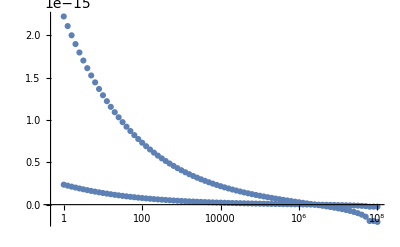

```mathematica
Show[{
ListLogLinearPlot[Table[{10^i,Da/.M->10^i},{i,0,8,0.1}]],
ListLogLinearPlot[Table[{10^i,Da$mod/.M->10^i},{i,0,8,0.1}]]
}]
```

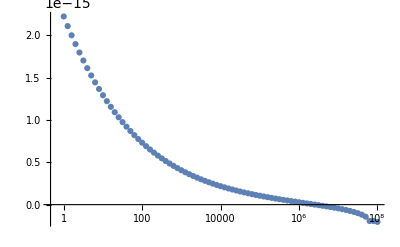

```mathematica
ListLogLinearPlot[Table[{10^i,Da$wlow/.M->10^i},{i,0,8,0.1}]]
```

```mathematica
NSolve[Da==0,M]
```

$Aborted

-Graphics3D-